```mathematica
SetOptions[EvaluationNotebook[],AutoGeneratedPackage->"AnSEL.m"]
```

# AnSEL - Analysis and Simplification of Equations with Loops

## Global variables

```mathematica
ModuleLoaded::dependency="The module `1` requires `2`, which has not been loaded.";

If[ModuleLoaded[FunKit]=!=True,
Message[ModuleLoaded::dependency,"FEDeriK","FunKit"];
Abort[];
];

If[ModuleLoaded[FEDeriK]=!=True,
Message[ModuleLoaded::dependency,"FEDeriK","FunKit"];
Abort[];
];

ModuleLoaded[AnSEL]=True;
```

```mathematica
$FunKitDirectory=SelectFirst[Join[{FileNameJoin[{$UserBaseDirectory,"Applications","FunKit"}],FileNameJoin[{$BaseDirectory,"Applications","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","Applications","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","Packages","FunKit"}],FileNameJoin[{$InstallationDirectory,"AddOns","ExtraPackages","FunKit"}]},Select[$Path,StringContainsQ[#,"FunKit"]&]],DirectoryQ[#]&]<>"/";
```

## Identification of expressions

```mathematica
Min
```

```mathematica
StartPoints[setup_,expr_FTerm]:=Module[{obj,count},
obj=Select[ExtractObjectsWithIndex[setup,expr],MemberQ[$indexedObjects,Head@#]&];
count=Counts[Map[Head,obj]];
Return[Values[count]]
]

TakeDerivatives[Setup,WetterichEquation,
{A[p,{a,b}],A[-p,{a,b}]}
][[1]];
%//Truncate[Setup,#]&;
%[[2]]
StartPoints[Setup,%]
```

FTerm[-1/2,Propagator[{cb,c},{ic$929,a$927}],GammaN[{c,cb,A},{-id$931,-ic$929,-eI897}],Propagator[{cb,c},{ic$930,id$931}],GammaN[{c,cb,A},{-id$932,-ic$930,-eI898}],Propagator[{cb,c},{b$928,id$932}],Rdot[{c,cb},{-a$927,-b$928}]]

<|Propagator→3,GammaN→2,Rdot→1|>

# Testing

```mathematica
Get["FunKit`"]
```

Loading modules...

...TensorBases loaded

...FEDeriK loaded

...AnSEL loaded

...DiANE loaded

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0
Year: 2025
For more information, call FunKitInfo[].

```mathematica
fields= <|
"cField"-> {
A[p,{v, c}],
{ϕ[p],ϕx[p]}
},
"Grassmann"->{
{cb[p,{c}],c[p,{c}]}
}
|>;
truncation=<|
GammaN->{
{A,A},{A,A,A},{A,A,A,A},
{A,cb,c}
},
Propagator->{
{A,A},{cb,c}
},
Rdot->{
{A,A},{cb,c}
}
|>
masterEquation={
{1/2 A[x]VBasis[{A,A},{-x,-y}]A[y]},
{-cb[x]VBasis[{cb,c},{-x,-y}],c[y]}
};
Setup:=<|
"MasterEquation"->masterEquation,
"FieldSpace"->fields,
"Truncation"->truncation
|>;
SetTexStyles[cb->"\\bar{c}"]
```

<|GammaN→{{A,A},{A,A,A},{A,A,A,A},{A,cb,c}},Propagator→{{A,A},{cb,c}},Rdot→{{A,A},{cb,c}}|>

```mathematica
ReduceIndices[Setup,
FEq[FTerm[
γ[{cb,c},{-x,-y}]GammaN[{cb,AnyField},{y,z}]γ[{AnyField,A},{-z,-g}],cb[x]
]]
]//FPrint[Setup,#]&
ReduceIndices[Setup,
FEq[FTerm[
γ[{AnyField,AnyField},{-aa,-bb}],γ[{cb,c},{-x,-y}]GammaN[{cb,AnyField},{y,z}]γ[{AnyField,A},{-z,-g}],b,c
]]
]
%//FPrint[Setup,#]&
```

-Graphics-

FEq[FTerm[-1,γ[{AnyField,AnyField},{-aa,-bb}],GammaN[{cb,AnyField},{-x,z}] γ[{AnyField,A},{-z,-g}],b,c]]

-Graphics-

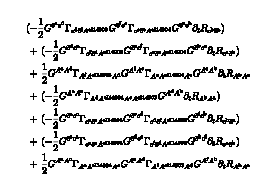

```mathematica
TakeDerivatives[Setup,WetterichEquation,
{A[p,{a,b}],A[-p,{a,b}]}
][[1]];
%//Truncate[Setup,#]&;
%//FPrint[Setup,#]&
```

```mathematica
ReduceIndices[setup_,term_FTerm]:=Module[
{closedSIndices,
cases,i,allObj,
subCase,subObj,subIndices,
subsubObj,
originalCases,result=term
},
(*TODO: TAKE CARE OF NESTED ENTRIES*)
closedSIndices=GetClosedSuperIndices[setup,term];

cases=Cases[term,γ[__],Infinity];
originalCases=cases;
cases[[All,1]]=Map[{{#[[1]]},{#[[2]]}}&,cases[[All,1]]];
cases[[All,2]]=Map[{{#[[1]]},{#[[2]]}}&,cases[[All,2]]];

(*The following code expands the γ[{f1,f2},{i1,i2}] into γ[{{f1,p[f1]},{f2,p[f2]}},{{i1,p[i1]},{i2,p[i2]}}], where the p[...] are the "partners", i.e. the matching indices somewhere else. If no partner exists, p[...]=0. This effectively marks open indices.*)
allObj=ExtractObjectsWithIndex[setup,term];
Do[
subIndices=Flatten[cases[[i,2,All]]]//.Times[-1,a_Symbol]:>a;
subObj=Select[allObj,(Or@@Table[MemberQ[#,subIndices[[j]],Infinity],{j,1,Length[subIndices]}])&];

Do[
subsubObj=Select[subObj,Head[#]=!=γ&&MemberQ[#,subIndices[[j]],Infinity]&];
If[Not[Length[subsubObj]<=1],Abort[]];

(*No partner exists*)
If[Not@MemberQ[closedSIndices,subIndices[[j]]],
AppendTo[cases[[i,1,j]],0];
AppendTo[cases[[i,2,j]],0];
Continue[]
];

(*Get the partner position*)
fIdx=FirstPosition[subsubObj[[1,2]]//.Times[-1,a_Symbol]:>a,subIndices[[j]]][[1]];
AppendTo[cases[[i,1,j]],subsubObj[[1,1,fIdx]]];
AppendTo[cases[[i,2,j]],-cases[[i,2,j,1]]];
,{j,1,Length[subIndices]}];

,{i,1,Length[cases]}];

(*Now, we use this information to reduce what we can*)
Do[
subCase=cases[[i]];

(*Let's start with the possible zero entries.*)
If[FreeQ[subCase[[1,1]],AnyField]&&
FreeQ[subCase[[1,1]],0]&&
subCase[[1,1,1]]=!=GetPartnerField[setup,subCase[[1,1,2]]],
result=result//.originalCases[[i]]:>0;
Continue[];
];
If[FreeQ[subCase[[1,2]],AnyField]&&
FreeQ[subCase[[1,2]],0]&&
subCase[[1,2,1]]=!=GetPartnerField[setup,subCase[[1,2,2]]],
result=result//.originalCases[[i]]:>0;
Continue[];
];
If[FreeQ[subCase[[1,All,1]],AnyField]&&
FreeQ[subCase[[1,All,1]],0]&&
subCase[[1,1,1]]=!=GetPartnerField[setup,subCase[[1,2,1]]],
result=result//.originalCases[[i]]:>0;
Continue[];
];

If[(Count[Flatten[subCase[[1]]],AnyField]+Count[Flatten[subCase[[1]]],0])===4,
Print["yet",subCase[[1]]]
];


If[Length[subCase[[1,1]]]===1&&Length[subCase[[1,2]]]===1,
Print["nope"];
Continue[]
];
repl={};
(*Then check the left index*)
If[Length[cases[[i,1,1]]]===2,
If[cases[[i,1,1,1]]===GetPartnerField[setup,cases[[i,1,1,2]]],
j
]
];
(*Then the right one*)
If[Length[cases[[i,1,2]]]===2,
If[cases[[i,1,2,1]]===GetPartnerField[setup,cases[[i,1,2,2]]],
Print["bye at ",cases[[i]]],

]
];
,{i,1,Length[cases]}
];

Print[cases];
Return[result];
];
ReduceIndices[setup_,eq_FEq]:=Module[{},
Map[ReduceIndices[setup,#]&,eq]
];
```